# Arm isometric response

## Import

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_05_31__10_53_09/";  (* Evolved *)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_02__12_08_19/"; (* Manual *)*)
SetDirectory[dirName];
all=Import["Isometric.txt", "Table"];
varNames=all[[1]];
data = all[[2;;-2]];
dims = Dimensions[all]
numVars=Dimensions[varNames]
numData=Length[data]
```

{322}

{112}

320

## Config

```mathematica
range = numData/2;
rangeElb = {1,range};
rangeShd={1+range, numData};
padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, PlotRange->All, ImagePadding->padds};
graphicsWidth = 600;
```

## Functions

```mathematica
NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_, range_]:=Table[data[[i,NtoI[name]]],{i,range[[1]],range[[2]]}];
NamePlot[name1_,name2_,range_, options_] := ListLinePlot[Transpose[{NtoD[name1,range],NtoD[name2,range]}], Join[plotOptions,options]];
DataPlot[data_,name_,range_, options_] := ListLinePlot[Transpose[{data,NtoD[name,range]}], Join[plotOptions,options]];
DataDataPlot[data1_,data2_,range_, options_] := ListLinePlot[Transpose[{data1,data2}], Join[plotOptions,options]];
```

## Draw arm kinematics

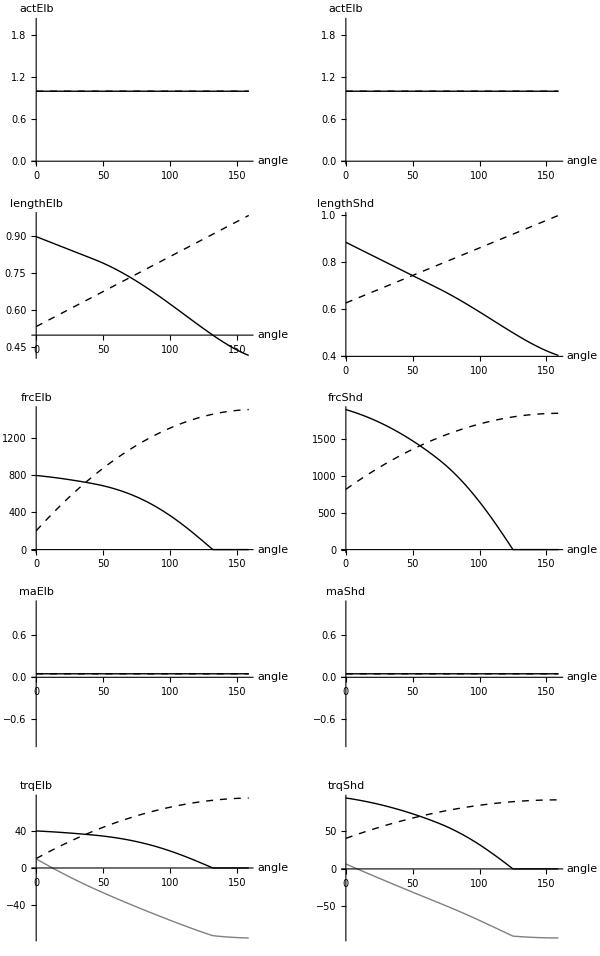

```mathematica
(* Joint angles *)
radToDeg = N[180 / Pi];
elbAng = NtoD["angleElbow",rangeElb] * radToDeg;
shdAng = NtoD["angleShoulder",rangeShd] * radToDeg;

(* Activations *)
actElbFl= DataPlot[elbAng,"ElbowFlexorAct",rangeElb,{PlotStyle->Black,AxesLabel->{"angle","actElb"}}];
actElbEx= DataPlot[elbAng,"ElbowExtensorAct",rangeElb,{PlotStyle->{Black,Dashed}}];
actElbPlot = Show[actElbFl, actElbEx];

actShdFl= DataPlot[shdAng,"ShoulderFlexorAct",rangeShd,{PlotStyle->Black,AxesLabel->{"angle","actElb"}}];
actShdEx= DataPlot[shdAng,"ShoulderExtensorAct",rangeShd,{PlotStyle->{Black,Dashed}}];
actShdPlot = Show[actShdFl, actShdEx];

(* Muscle lengths *)
m1Elb= DataPlot[elbAng,"ElbowFlexorLengthNorm",rangeElb,{PlotStyle->Black,AxesLabel->{"angle","lengthElb"}}];
m2Elb= DataPlot[elbAng,"ElbowExtensorLengthNorm",rangeElb,{PlotStyle->{Black,Dashed}}];
elbMusclePlot = Show[m1Elb, m2Elb];

m1Shd= DataPlot[shdAng,"ShoulderFlexorLengthNorm",rangeShd,{PlotStyle->Black,AxesLabel->{"angle","lengthShd"}}];
m2Shd= DataPlot[shdAng,"ShoulderExtensorLengthNorm",rangeShd,{PlotStyle->{Black,Dashed}}];
shdMusclePlot = Show[m1Shd, m2Shd];

(* Force *)
forceElbFl= DataPlot[elbAng,"ElbowFlexorForce",rangeElb,{PlotStyle->Black,AxesLabel->{"angle","frcElb"}}];
forceElbEx= DataPlot[elbAng,"ElbowExtensorForce",rangeElb,{PlotStyle->{Black,Dashed}}];
elbForcePlot = Show[forceElbFl, forceElbEx];

forceShdFl= DataPlot[shdAng,"ShoulderFlexorForce",rangeShd,{PlotStyle->Black,AxesLabel->{"angle","frcShd"}}];
forceShdEx= DataPlot[shdAng,"ShoulderExtensorForce",rangeShd,{PlotStyle->{Black,Dashed}}];
shdForcePlot = Show[forceShdFl, forceShdEx];

(* Moment arms *)
maElbFl= DataPlot[elbAng,"ElbowFlexorMomentArm",rangeElb,{PlotStyle->Black,AxesLabel->{"angle","maElb"}}];
maElbEx= DataPlot[elbAng,"ElbowExtensorMomentArm",rangeElb,{PlotStyle->{Black,Dashed}}];
elbMaPlot = Show[maElbFl, maElbEx];

maShdFl= DataPlot[shdAng,"ShoulderFlexorMomentArm",rangeShd,{PlotStyle->Black,AxesLabel->{"angle","maShd"}}];
maShdEx= DataPlot[shdAng,"ShoulderExtensorMomentArm",rangeShd,{PlotStyle->{Black,Dashed}}];
shdMaPlot = Show[maShdFl, maShdEx];

(* Torques *)
trqElbFlD = NtoD["ElbowFlexorTorque",rangeElb];
trqElbExD = NtoD["ElbowExtensorTorque",rangeElb];
trqShdFlD = NtoD["ShoulderFlexorTorque",rangeShd];
trqShdExD = NtoD["ShoulderExtensorTorque",rangeShd];
elbNet = 0.5*trqElbFlD - trqElbExD;
shdNet = 0.5*trqShdFlD - trqShdExD;

clcTrqElbFlD = NtoD["ElbowFlexorMomentArm", rangeElb] * NtoD["ElbowFlexorForce", rangeElb];

trqElbFl =DataDataPlot[elbAng,trqElbFlD,rangeElb, {PlotStyle->Black,AxesLabel->{"angle","trqElb"}}];
trqElbEx =DataDataPlot[elbAng,trqElbExD,rangeElb,{PlotStyle->{Black,Dashed}}];
trqElbNet =DataDataPlot[elbAng,elbNet,rangeElb,{PlotStyle->{Gray}}];
trqShdFl =DataDataPlot[shdAng,trqShdFlD,rangeElb,{PlotStyle->Black,AxesLabel->{"angle","trqShd"}}];
trqShdEx =DataDataPlot[shdAng,trqShdExD,rangeElb,{PlotStyle->{Black,Dashed}}];
trqShdNet =DataDataPlot[shdAng,shdNet,rangeShd,{PlotStyle->{Gray}}];
trqPlotElb = Show[trqElbFl, trqElbEx, trqElbNet];
trqPlotShd = Show[trqShdFl, trqShdEx, trqShdNet];



elbAng;
elbLength=NtoD["ElbowExtensorLengthNorm",rangeElb];
m = Min[elbLength];

grid = GraphicsGrid[{{actElbPlot, actShdPlot},{elbMusclePlot,shdMusclePlot},{elbForcePlot,shdForcePlot},{elbMaPlot,shdMaPlot},{trqPlotElb,trqPlotShd}},ImageSize->graphicsWidth]
```